# Omid Amir Index

## Slide Show Subtitle

Baoxiang Pan
8.7.2017

## Materials

Precipitation (GPCP)

```mathematica
precip=Import["/Users/lambda/Documents/Wolfram Mathematica/Omid-Amir-Index/data/CAMonthTotal.txt","List"];
```

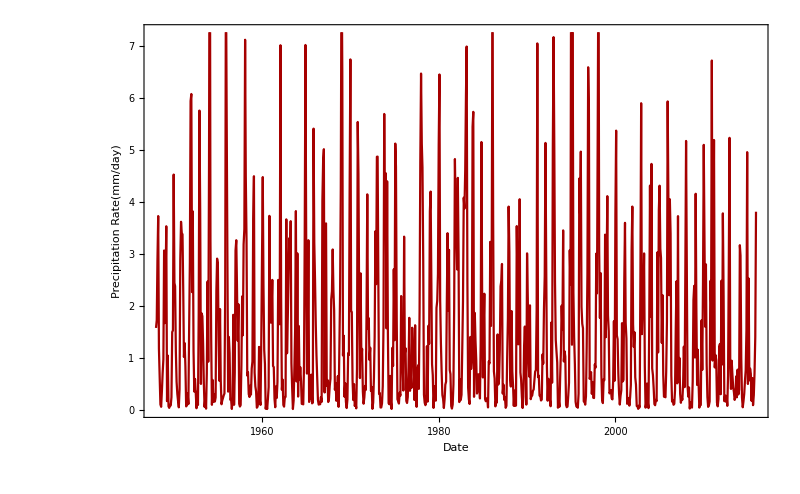

```mathematica
DateListPlot[TimeSeries[precip,{{1948,1,1},Automatic,"Month"}],
	BaseStyle->20,
	FrameLabel->{"Date","Precipitation Rate(mm/day)"},
	ImageSize->800]
```

```mathematica
wprecip=Table[Total[precip[[10+year;;15+year]]],{year,0,Length[precip]/12}];
Length[wprecip]
```

69

## Numerical Experiments

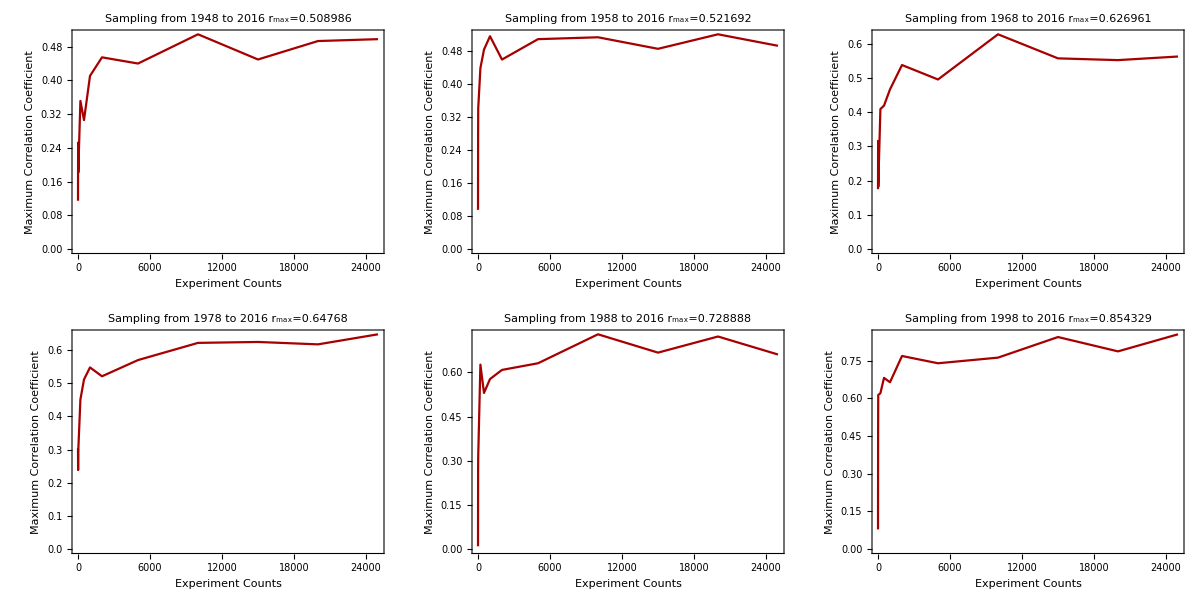

```mathematica
Grid[ArrayReshape[Table[Block[{sprecip=wprecip[[point-1947;;]],data,max},
	data=Table[{sample,Max[Table[Abs[Correlation[RandomReal[{0,1},Length[sprecip]],sprecip]],{i,sample}]]},
	{sample,{1,10,20,200,500,1000,2000,5000,10000,15000,20000,25000}}];
	max=Max[Map[#[[2]]&,data]];
ListLinePlot[data,
	ImageSize->400,
	PlotLabel->"Sampling from  "<>ToString[point]<>" to 2016\n r_max="<>ToString[max],
	Frame->True,BaseStyle->13,FrameLabel->{"Experiment Counts","Maximum Correlation Coefficient"}]],
	{point,1948,1998,10}],{2,3}]]
```

## Using Air Temperature as Predictor

```mathematica
T=Import["/Volumes/lambda/backup/Documents/Code/CaliforniaDrought2016/Data/SST/NCEP_air.mon.mean.nc",
					{"Datasets","air"}];
lat=Import["/Volumes/lambda/backup/Documents/Code/CaliforniaDrought2016/Data/SST/NCEP_air.mon.mean.nc",
					{"Datasets","lat"}];
lon=Import["/Volumes/lambda/backup/Documents/Code/CaliforniaDrought2016/Data/SST/NCEP_air.mon.mean.nc",
					{"Datasets","lon"}];
```

```mathematica
MaxCorrelation[lag_,start_]:=Block[{corr,
									position,
									TT=T[[12*(start-1)+1;;,;;,;;]],
									wwprecip=wprecip[[start;;]]},
	corr=Abs[If[lag<10,
		Table[Table[Correlation[TT[[10-lag;;Length[TT];;12,i,j]],wwprecip],{i,Dimensions[TT][[2]]}],
			{j,Dimensions[TT][[3]]}],
		Table[Table[Correlation[TT[[22-lag;;Length[TT];;12,i,j]][[1;;Length[wwprecip[[2;;]]]]],
								wwprecip[[2;;]]],{i,Dimensions[TT][[2]]}],
			{j,Dimensions[TT][[3]]}]]];
	position=Position[corr,Max[corr]];
	{lag,lat[[position[[1,2]]]],lon[[position[[1,1]]]],Max[corr]}]
```

```mathematica
TableForm[Table[MaxCorrelation[lag,40],{lag,1,12}],
TableHeadings->{None,{"lagging","lat","lon","r"}},TableAlignments->Center]
```

lagging | lat | lon | r
1 | 2.5 | 70. | 0.606371
2 | -20. | 290. | 0.648349
3 | 55. | 192.5 | 0.661585
4 | 57.5 | 197.5 | 0.65516
5 | -10. | 337.5 | 0.651668
6 | 17.5 | 240. | 0.68494
7 | 57.5 | 197.5 | 0.639583
8 | 70. | 27.5 | 0.691709
9 | -55. | 117.5 | 0.601838
10 | 7.5 | 350. | 0.594153
11 | -20. | 292.5 | 0.664195
12 | -20. | 292.5 | 0.815678

```mathematica
TableForm[Table[MaxCorrelation[lag,36],{lag,1,12}],
TableHeadings->{None,{"lagging","lat","lon","r"}},TableAlignments->Center]
```

lagging | lat | lon | r
1 | -77.5 | 290. | 0.610462
2 | -20. | 290. | 0.676351
3 | 57.5 | 195. | 0.628815
4 | -12.5 | 342.5 | 0.570728
5 | 12.5 | 50. | 0.556415
6 | 45. | 235. | 0.61503
7 | 55. | 192.5 | 0.530481
8 | 67.5 | 30. | 0.585403
9 | -25. | 147.5 | 0.595418
10 | -45. | 287.5 | 0.550239
11 | 35. | 312.5 | 0.540056
12 | 35. | 10. | 0.579997

```mathematica
TableForm[Table[MaxCorrelation[lag,32],{lag,1,12}],
TableHeadings->{None,{"lagging","lat","lon","r"}},TableAlignments->Center]
```

lagging | lat | lon | r
1 | 22.5 | 60. | 0.554281
2 | -20. | 290. | 0.618773
3 | 57.5 | 195. | 0.628058
4 | 60. | 185. | 0.591376
5 | -62.5 | 57.5 | 0.528651
6 | 57.5 | 197.5 | 0.605209
7 | 55. | 192.5 | 0.502935
8 | 65. | 52.5 | 0.499954
9 | -25. | 147.5 | 0.561978
10 | 50. | 232.5 | 0.494303
11 | 35. | 312.5 | 0.515041
12 | -20. | 290. | 0.577188

```mathematica
TableForm[Table[MaxCorrelation[lag,10],{lag,1,12}],
TableHeadings->{None,{"lagging","lat","lon","r"}},TableAlignments->Center]
```

lagging | lat | lon | r
1 | 22.5 | 60. | 0.507005
2 | -7.5 | 337.5 | 0.472155
3 | 57.5 | 195. | 0.557621
4 | 60. | 187.5 | 0.591615
5 | 57.5 | 190. | 0.464187
6 | 55. | 200. | 0.528788
7 | -10. | 332.5 | 0.450616
8 | -27.5 | 150. | 0.414123
9 | -25. | 147.5 | 0.444578
10 | -77.5 | 255. | 0.439542
11 | 35. | 315. | 0.40806
12 | 40. | 242.5 | 0.49691

```mathematica
TableForm[Table[MaxCorrelation[lag,15],{lag,1,12}],
TableHeadings->{None,{"lagging","lat","lon","r"}},TableAlignments->Center]
```

lagging | lat | lon | r
1 | 22.5 | 60. | 0.49586
2 | -7.5 | 337.5 | 0.484735
3 | 57.5 | 195. | 0.55518
4 | 60. | 187.5 | 0.594082
5 | 57.5 | 190. | 0.467587
6 | 55. | 200. | 0.532563
7 | -10. | 332.5 | 0.453303
8 | -27.5 | 150. | 0.417472
9 | -25. | 147.5 | 0.437048
10 | -57.5 | 102.5 | 0.447879
11 | 35. | 315. | 0.440545
12 | 35. | 302.5 | 0.547553

```mathematica
TableForm[Table[MaxCorrelation[lag,5],{lag,1,12}],
TableHeadings->{None,{"lagging","lat","lon","r"}},TableAlignments->Center]
```

lagging | lat | lon | r
1 | 22.5 | 60. | 0.494227
2 | -7.5 | 337.5 | 0.520937
3 | -7.5 | 337.5 | 0.509635
4 | 60. | 187.5 | 0.549182
5 | -10. | 335. | 0.48837
6 | -10. | 352.5 | 0.556021
7 | -10. | 332.5 | 0.512611
8 | -77.5 | 165. | 0.434163
9 | -10. | 332.5 | 0.447486
10 | -77.5 | 255. | 0.49067
11 | -2.5 | 317.5 | 0.405717
12 | 40. | 245. | 0.503847

## Using SLP as Predictor

```mathematica
SLP=Import["/Volumes/lambda/backup/Documents/Code/CaliforniaDrought2016/Data/Pressure/slp.mon.mean.nc",
					{"Datasets","slp"}];
lat=Import["/Volumes/lambda/backup/Documents/Code/CaliforniaDrought2016/Data/Pressure/slp.mon.mean.nc",
					{"Datasets","lat"}];
lon=Import["/Volumes/lambda/backup/Documents/Code/CaliforniaDrought2016/Data/Pressure/slp.mon.mean.nc",
					{"Datasets","lon"}];
```

```mathematica
MaxCorrelation[lag_,start_]:=Block[{corr,
									position,
									TT=SLP[[12*(start-1)+1;;,;;,;;]],
									wwprecip=wprecip[[start;;]]},
	corr=Abs[If[lag<10,
		Table[Table[Correlation[TT[[10-lag;;Length[TT];;12,i,j]],wwprecip],{i,Dimensions[TT][[2]]}],
			{j,Dimensions[TT][[3]]}],
		Table[Table[Correlation[TT[[22-lag;;Length[TT];;12,i,j]][[1;;Length[wwprecip[[2;;]]]]],
								wwprecip[[2;;]]],{i,Dimensions[TT][[2]]}],
			{j,Dimensions[TT][[3]]}]]];
	position=Position[corr,Max[corr]];
	{lag,lat[[position[[1,2]]]],lon[[position[[1,1]]]],Max[corr]}]
```

```mathematica
TableForm[Table[MaxCorrelation[lag,1],{lag,1,12}],
TableHeadings->{None,{"lagging","lat","lon","r"}},TableAlignments->Center]
```

lagging | lat | lon | r
1 | -20. | 292.5 | 0.440482
2 | 62.5 | 252.5 | 0.394972
3 | 20. | 250. | 0.37725
4 | -30. | 347.5 | 0.396494
5 | -35. | 345. | 0.411944
6 | -17.5 | 202.5 | 0.458282
7 | -22.5 | 325. | 0.439733
8 | -17.5 | 52.5 | 0.385868
9 | -55. | 12.5 | 0.313723
10 | -85. | 95. | 0.452468
11 | -20. | 292.5 | 0.511367
12 | -20. | 292.5 | 0.495193

```mathematica
TableForm[Table[MaxCorrelation[lag,5],{lag,1,12}],
TableHeadings->{None,{"lagging","lat","lon","r"}},TableAlignments->Center]
```

lagging | lat | lon | r
1 | -20. | 292.5 | 0.44546
2 | 62.5 | 252.5 | 0.397146
3 | 20. | 250. | 0.396587
4 | 55. | 317.5 | 0.41525
5 | -35. | 345. | 0.435685
6 | -17.5 | 202.5 | 0.456321
7 | -22.5 | 325. | 0.459848
8 | -15. | 52.5 | 0.405058
9 | -55. | 12.5 | 0.327957
10 | -85. | 95. | 0.467375
11 | -20. | 292.5 | 0.553928
12 | -20. | 292.5 | 0.49871

```mathematica
TableForm[Table[MaxCorrelation[lag,15],{lag,1,12}],
TableHeadings->{None,{"lagging","lat","lon","r"}},TableAlignments->Center]
```

lagging | lat | lon | r
1 | -20. | 292.5 | 0.4378
2 | 15. | 22.5 | 0.510749
3 | 20. | 250. | 0.430531
4 | 62.5 | 225. | 0.446911
5 | -35. | 345. | 0.441456
6 | 45. | 280. | 0.51594
7 | -20. | 325. | 0.49595
8 | -15. | 52.5 | 0.449405
9 | 42.5 | 87.5 | 0.402903
10 | -85. | 92.5 | 0.422007
11 | -20. | 292.5 | 0.585729
12 | -20. | 292.5 | 0.515599

```mathematica
TableForm[Table[MaxCorrelation[lag,25],{lag,1,12}],
TableHeadings->{None,{"lagging","lat","lon","r"}},TableAlignments->Center]
```

lagging | lat | lon | r
1 | 30. | 25. | 0.48408
2 | 15. | 20. | 0.566774
3 | 20. | 250. | 0.444045
4 | 62.5 | 227.5 | 0.514818
5 | 12.5 | 345. | 0.52141
6 | 45. | 280. | 0.485652
7 | -20. | 322.5 | 0.53257
8 | -12.5 | 52.5 | 0.497694
9 | 45. | 85. | 0.438659
10 | -85. | 90. | 0.431801
11 | -20. | 292.5 | 0.615843
12 | -20. | 292.5 | 0.543293

```mathematica
TableForm[Table[MaxCorrelation[lag,36],{lag,1,12}],
TableHeadings->{None,{"lagging","lat","lon","r"}},TableAlignments->Center]
```

lagging | lat | lon | r
1 | 37.5 | 30. | 0.549616
2 | 15. | 10. | 0.630124
3 | 30. | 247.5 | 0.52951
4 | 55. | 320. | 0.533081
5 | -55. | 165. | 0.587665
6 | 45. | 275. | 0.525992
7 | -22.5 | 315. | 0.556996
8 | -10. | 57.5 | 0.479894
9 | 42.5 | 90. | 0.664766
10 | -12.5 | 347.5 | 0.505072
11 | -20. | 292.5 | 0.716987
12 | -20. | 292.5 | 0.579788

```mathematica
TableForm[Table[MaxCorrelation[lag,40],{lag,1,12}],
TableHeadings->{None,{"lagging","lat","lon","r"}},TableAlignments->Center]
```

lagging | lat | lon | r
1 | 37.5 | 30. | 0.599984
2 | 10. | 17.5 | 0.67744
3 | 30. | 250. | 0.692047
4 | 17.5 | 217.5 | 0.64275
5 | -85. | 80. | 0.601089
6 | 17.5 | 235. | 0.640243
7 | -10. | 297.5 | 0.561771
8 | 45. | 292.5 | 0.503838
9 | 42.5 | 90. | 0.646956
10 | 50. | 155. | 0.564167
11 | -20. | 292.5 | 0.704752
12 | 12.5 | 10. | 0.731042

```mathematica
Position[lat,-20.]
Position[lon,292.5]
```

{{45}}

{{118}}

```mathematica
cSLP=SLP[[;;,45,118]];
```

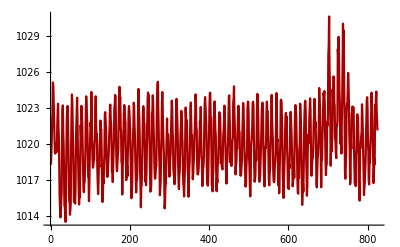

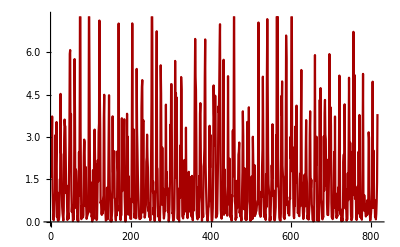

```mathematica
ListLinePlot[cSLP]
ListLinePlot[precip]
```

```mathematica
Correlation[cSLP[[1;;Length[precip]]],precip]
```

-0.535318